```mathematica
H:=Function[{Δ,ξ,t},
-1/2(Δ+ξ)PauliMatrix[3]+f[t]/2 PauliMatrix[1]
];
```

```mathematica
HNum:=Function[{Δ,ξ,θ,tg,t},
-1/2(Δ+ξ)PauliMatrix[3]+θ/(2 tg)(1-Cos[2π t/tg])PauliMatrix[1]
];
```

```mathematica
com:=#1.#2-#2.#1&;
```

```mathematica
ρ=({{ρ00Re+ⅈ ρ00Im, ρ01Re+ⅈ ρ01Im}, {ρ10Re+ⅈ ρ10Im, ρ11Re+ⅈ ρ11Im}});
(*ρ=({{ρ00, ρ01}, {ρ10, ρ11}});*)
```

```mathematica
rhs=-ⅈ com[H[Δ,ξ,t],ρ];
```

```mathematica
ComplexExpand[rhs]
```

{{-1/2 ρ01Im f[t]+1/2 ρ10Im f[t]+ⅈ (1/2 ρ01Re f[t]-1/2 ρ10Re f[t]),-Δ ρ01Im-ξ ρ01Im-1/2 ρ00Im f[t]+1/2 ρ11Im f[t]+ⅈ (Δ ρ01Re+ξ ρ01Re+1/2 ρ00Re f[t]-1/2 ρ11Re f[t])},{Δ ρ10Im+ξ ρ10Im+1/2 ρ00Im f[t]-1/2 ρ11Im f[t]+ⅈ (-Δ ρ10Re-ξ ρ10Re-1/2 ρ00Re f[t]+1/2 ρ11Re f[t]),1/2 ρ01Im f[t]-1/2 ρ10Im f[t]+ⅈ (-1/2 ρ01Re f[t]+1/2 ρ10Re f[t])}}

```mathematica
rhsRe = FullSimplify[Re[rhs],Assumptions->Δ ∈ Reals && ξ ∈ Reals && f[t]>=0&& ρ00Re∈ Reals && ρ00Im∈ Reals && ρ01Re∈ Reals && ρ01Im∈ Reals && ρ10Re∈ Reals && ρ10Im∈ Reals && ρ11Re∈ Reals && ρ11Im∈ Reals ]
```

{{1/2 (-ρ01Im+ρ10Im) f[t],-((Δ+ξ) ρ01Im)+1/2 (-ρ00Im+ρ11Im) f[t]},{(Δ+ξ) ρ10Im+1/2 (ρ00Im-ρ11Im) f[t],1/2 (ρ01Im-ρ10Im) f[t]}}

```mathematica
rhsIm =FullSimplify[Im[rhs],Assumptions->Δ ∈ Reals && ξ ∈ Reals && f[t]>=0&& ρ00Re∈ Reals && ρ00Im∈ Reals && ρ01Re∈ Reals && ρ01Im∈ Reals && ρ10Re∈ Reals && ρ10Im∈ Reals && ρ11Re∈ Reals && ρ11Im∈ Reals ]
```

{{1/2 (ρ01Re-ρ10Re) f[t],(Δ+ξ) ρ01Re+1/2 (ρ00Re-ρ11Re) f[t]},{-((Δ+ξ) ρ10Re)+1/2 (-ρ00Re+ρ11Re) f[t],1/2 (-ρ01Re+ρ10Re) f[t]}}

```mathematica
rhsReNon=rhsRe/. {Δ->0,ξ->0}
rhsImNon=rhsIm/. {Δ->0,ξ->0}
```

{{1/2 (-ρ01Im+ρ10Im) f[t],1/2 (-ρ00Im+ρ11Im) f[t]},{1/2 (ρ00Im-ρ11Im) f[t],1/2 (ρ01Im-ρ10Im) f[t]}}

{{1/2 (ρ01Re-ρ10Re) f[t],1/2 (ρ00Re-ρ11Re) f[t]},{1/2 (-ρ00Re+ρ11Re) f[t],1/2 (-ρ01Re+ρ10Re) f[t]}}

```mathematica
(*Step 1:Set global assumptions for initial variables*)
$Assumptions1={t∈Reals&&ωq∈Reals&&ωd∈Reals&&ζ∈Reals&&f[t]>=0};

(*Step 2:Define the Hamiltonian in the lab frame*)
(*Hlab= (ωq+ζ)/2*PauliMatrix[3]+f[t]*Cos[ωd*t]*PauliMatrix[1];*)
Hlab= (ωq+ζ)/2*PauliMatrix[3]+1/2 f[t]*(ⅇ^(ⅈ ωd t)+ⅇ^(-ⅈ ωd t))*PauliMatrix[1];

(*Step 3:Define the transformation matrix S*)
S=MatrixExp[-ⅈ*(ωd*t/2)*PauliMatrix[3]];

(*Step 4:Compute the conjugate transpose of S*)
SConjugate=ConjugateTranspose[S];

(*Step 5:Compute the time derivative of S*)
dSdt=D[S,t];

(*Step 6:Calculate the derivative term for the rotating frame transformation*)
DerivativeTerm=-ⅈ*SConjugate.dSdt;

(*Step 7:Calculate the Hamiltonian in the rotating frame,HRF*)
HRF=ExpToTrig[FullSimplify[SConjugate.Hlab.S+DerivativeTerm,Assumptions->$Assumptions1]];

(*Step 8:Apply the rotating wave approximation (RWA)*)
HRFRWA=HRF/. {Cos[2*ωd*t]->0,Sin[2*ωd*t]->0};
HRFRWA=FullSimplify[HRFRWA,Assumptions->$Assumptions1];
HRFRWA=ExpToTrig[HRFRWA];

(*Step 9:Set assumptions for density matrix components*)
$Assumptions2={$Assumptions1&&ρ00Re∈Reals&&ρ01Re∈Reals&&ρ10Re∈Reals&&ρ11Re∈Reals&&ρ00Im∈Reals&&ρ01Im∈Reals&&ρ10Im∈Reals&&ρ11Im∈Reals};

(*Step 10:Define the density matrix ρ*)
ρ={{ρ00Re+ⅈ*ρ00Im,ρ01Re+ⅈ*ρ01Im},{ρ10Re+ⅈ*ρ10Im,ρ11Re+ⅈ*ρ11Im}};

(*Step 11:Compute the time derivative of the density matrix in the rotating frame*)
dρdt=FullSimplify[-ⅈ*(Dot[HRFRWA,ρ]-Dot[ρ,HRFRWA]),Assumptions-> Δ ∈ Reals && ζ ∈ Reals && f[t]>=0&& ρ00Re∈ Reals && ρ00Im∈ Reals && ρ01Re∈ Reals && ρ01Im∈ Reals && ρ10Re∈ Reals && ρ10Im∈ Reals && ρ11Re∈ Reals && ρ11Im∈ Reals &&ρ00Re∈Reals&&ρ01Re∈Reals&&ρ10Re∈Reals&&ρ11Re∈Reals&&ρ00Im∈Reals&&ρ01Im∈Reals&&ρ10Im∈Reals&&ρ11Im∈Reals];

(*Step 12:Perform the substitution ωq-ωd->Delta in the final results*)
HRFRWA=FullSimplify[HRFRWA]/. {ωq-ωd->Δ , ωd-ωq->-Δ};
dρdt=dρdt/. {ωq-ωd->Δ};

(*Display the results in matrix form*)
MatrixForm[FullSimplify[HRFRWA]];
MatrixForm[FullSimplify[(Δ+ζ)/2 * PauliMatrix[3] + f[t]/2 * PauliMatrix[1]]]
MatrixForm[dρdt]

(*Check*)
HRFRWA === FullSimplify[(Δ+ζ)/2 * PauliMatrix[3] + f[t]/2 * PauliMatrix[1]];
```

((Δ+ζ)/2 | f[t]/2
f[t]/2 | 1/2 (-Δ-ζ))

(1/2 (-ρ01Im+ⅈ ρ01Re+ρ10Im-ⅈ ρ10Re) f[t] | (Δ+ζ) (ρ01Im-ⅈ ρ01Re)+1/2 (-ρ00Im+ⅈ ρ00Re+ρ11Im-ⅈ ρ11Re) f[t]
-((Δ+ζ) (ρ10Im-ⅈ ρ10Re))+1/2 (ρ00Im-ⅈ ρ00Re-ρ11Im+ⅈ ρ11Re) f[t] | 1/2 (ρ01Im-ⅈ ρ01Re-ρ10Im+ⅈ ρ10Re) f[t])

## Numerical Solution Using the Liouville-von Neuman

```mathematica
ρSol:=Function[{θ,tg,ρ0},
ρ1[t]/.First[NDSolve[{ρ1'[t]== -ⅈ com[HNum[0,0,θ,tg,t],ρ1[t]],ρ1[0]==ρ0},ρ1,{t,0,tg}]]
];
```

```mathematica
θ=π/2;
tg=1;
ρ0=({{1, 0}, {0, 0}});
ρSolNum[t_]=ρSol[θ,tg,ρ0];
```

## Analytical Solution Using Superoperator formalism

```mathematica
DSolve[{L'[t]==(ⅈ θ/(2tg)(1-Cos[2π t/tg])({{0, -1, 1, 0}, {-1, 0, 0, 1}, {1, 0, 0, -1}, {0, 1, -1, 0}})).L[t],L[0]==IdentityMatrix[4]},L,t]
```

DSolve[{L'[t]=={{0,-1/4 ⅈ π (1-Cos[2 π t]),1/4 ⅈ π (1-Cos[2 π t]),0},{-1/4 ⅈ π (1-Cos[2 π t]),0,0,1/4 ⅈ π (1-Cos[2 π t])},{1/4 ⅈ π (1-Cos[2 π t]),0,0,-1/4 ⅈ π (1-Cos[2 π t])},{0,1/4 ⅈ π (1-Cos[2 π t]),-1/4 ⅈ π (1-Cos[2 π t]),0}}.L[t],L[0]=={{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}},L,t]

```mathematica
MatrixExp[Integrate[ⅈ θ/(2tg)(1-Cos[2π t1/tg])({{0, -1, 1, 0}, {-1, 0, 0, 1}, {1, 0, 0, -1}, {0, 1, -1, 0}}),{t1,0,t}]]//FullSimplify//MatrixForm
```

(Cos[1/8 (2 π t-Sin[2 π t])]^2 | -1/2 ⅈ Sin[1/4 (2 π t-Sin[2 π t])] | 1/2 ⅈ Sin[1/4 (2 π t-Sin[2 π t])] | Sin[1/8 (2 π t-Sin[2 π t])]^2
-1/2 ⅈ Sin[1/4 (2 π t-Sin[2 π t])] | Cos[1/8 (2 π t-Sin[2 π t])]^2 | Sin[1/8 (2 π t-Sin[2 π t])]^2 | 1/2 ⅈ Sin[1/4 (2 π t-Sin[2 π t])]
1/2 ⅈ Sin[1/4 (2 π t-Sin[2 π t])] | Sin[1/8 (2 π t-Sin[2 π t])]^2 | Cos[1/8 (2 π t-Sin[2 π t])]^2 | -1/2 ⅈ Sin[1/4 (2 π t-Sin[2 π t])]
Sin[1/8 (2 π t-Sin[2 π t])]^2 | 1/2 ⅈ Sin[1/4 (2 π t-Sin[2 π t])] | -1/2 ⅈ Sin[1/4 (2 π t-Sin[2 π t])] | Cos[1/8 (2 π t-Sin[2 π t])]^2)

```mathematica
LAnalytics:=Function[{θ,tg,t},
({{Cos[1/4 θ ((2 t)/tg-Sin[(2 π t)/tg]/π)]^2, -1/2 ⅈ Sin[(t θ)/tg-(θ Sin[(2 π t)/tg])/(2 π)], 1/2 ⅈ Sin[(t θ)/tg-(θ Sin[(2 π t)/tg])/(2 π)], Sin[1/4 θ ((2 t)/tg-Sin[(2 π t)/tg]/π)]^2}, {-1/2 ⅈ Sin[(t θ)/tg-(θ Sin[(2 π t)/tg])/(2 π)], Cos[1/4 θ ((2 t)/tg-Sin[(2 π t)/tg]/π)]^2, Sin[1/4 θ ((2 t)/tg-Sin[(2 π t)/tg]/π)]^2, 1/2 ⅈ Sin[(t θ)/tg-(θ Sin[(2 π t)/tg])/(2 π)]}, {1/2 ⅈ Sin[(t θ)/tg-(θ Sin[(2 π t)/tg])/(2 π)], Sin[1/4 θ ((2 t)/tg-Sin[(2 π t)/tg]/π)]^2, Cos[1/4 θ ((2 t)/tg-Sin[(2 π t)/tg]/π)]^2, -1/2 ⅈ Sin[(t θ)/tg-(θ Sin[(2 π t)/tg])/(2 π)]}, {Sin[1/4 θ ((2 t)/tg-Sin[(2 π t)/tg]/π)]^2, 1/2 ⅈ Sin[(t θ)/tg-(θ Sin[(2 π t)/tg])/(2 π)], -1/2 ⅈ Sin[(t θ)/tg-(θ Sin[(2 π t)/tg])/(2 π)], Cos[1/4 θ ((2 t)/tg-Sin[(2 π t)/tg]/π)]^2}})
];
```

```mathematica
LAnalytics[π/2,1,t].({{1}, {0}, {0}, {0}})
```

{{Cos[1/8 π (2 t-Sin[2 π t]/π)]^2},{-1/2 ⅈ Sin[(π t)/2-1/4 Sin[2 π t]]},{1/2 ⅈ Sin[(π t)/2-1/4 Sin[2 π t]]},{Sin[1/8 π (2 t-Sin[2 π t]/π)]^2}}

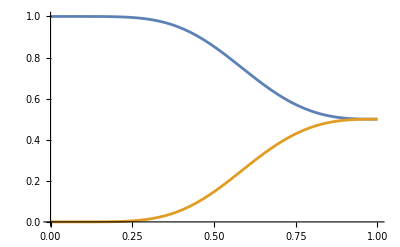

```mathematica
Plot[{Cos[1/8 π (2 t-Sin[2 π t]/π)]^2,Sin[1/8 π (2 t-Sin[2 π t]/π)]^2},{t,0,1}]
```

```mathematica
(* converting the von Neuman equation into a superoperator; the density matrix becomes a "vector"*)
comtosup[x_,n_]:=ⅈ (KroneckerProduct[Transpose[x],IdentityMatrix[n]]-KroneckerProduct[IdentityMatrix[n],x]);
(* converting the Lindblad operators into Lindblad superoperator *)
diss[x_,n_]:= KroneckerProduct[x*,x]-1/2 KroneckerProduct[Transpose[x].Conjugate[x],IdentityMatrix[n]]-1/2 KroneckerProduct[IdentityMatrix[n],ConjugateTranspose[x].x];
(* converting any operator acting on a density matrix into a superoperator *)
optosup[x_]:=KroneckerProduct[Conjugate[x],x];
DensMatToVec:=Flatten[Transpose[#],1]&;
DensVecToMat:=Transpose[ArrayReshape[Flatten[Transpose[#1],1],{#2,#2}]]&;
```

```mathematica
compdt = comtosup[HRFRWA, 2]//MatrixForm
FullSimplify[compdt, Assumptions->Δ ∈ Reals && ζ ∈ Reals && f[t]>=0&& ρ00Re∈ Reals && ρ00Im∈ Reals && ρ01Re∈ Reals && ρ01Im∈ Reals && ρ10Re∈ Reals && ρ10Im∈ Reals && ρ11Re∈ Reals && ρ11Im∈ Reals &&ρ00Re∈Reals&&ρ01Re∈Reals&&ρ10Re∈Reals&&ρ11Re∈Reals&&ρ00Im∈Reals&&ρ01Im∈Reals&&ρ10Im∈Reals&&ρ11Im∈Reals]
```

```mathematica
ρ1=({{ρ11, ρ12}, {ρ21, ρ22}});
```

```mathematica
ρ1Vec=DensMatToVec[ρ1];
```

```mathematica
DensVecToMat[({{ⅈ (1/2 (-Δ-ζ)+(Δ+ζ)/2), -1/2 ⅈ f[t], 1/2 ⅈ f[t], 0}, {-1/2 ⅈ f[t], ⅈ (Δ+ζ), 0, 1/2 ⅈ f[t]}, {1/2 ⅈ f[t], 0, ⅈ (-Δ-ζ), -1/2 ⅈ f[t]}, {0, 1/2 ⅈ f[t], -1/2 ⅈ f[t], ⅈ (1/2 (-Δ-ζ)+(Δ+ζ)/2)}}).ρ1Vec,2]//FullSimplify//MatrixForm
```

(1/2 ⅈ (ρ12-ρ21) f[t] | -1/2 ⅈ (2 (Δ+ζ) ρ12+(-ρ11+ρ22) f[t])
1/2 ⅈ (2 (Δ+ζ) ρ21+(-ρ11+ρ22) f[t]) | -1/2 ⅈ (ρ12-ρ21) f[t])

```mathematica
-ⅈ com[HRFRWA,ρ1]//FullSimplify//MatrixForm
```

(1/2 ⅈ (ρ12-ρ21) f[t] | -1/2 ⅈ (2 (Δ+ζ) ρ12+(-ρ11+ρ22) f[t])
1/2 ⅈ (2 (Δ+ζ) ρ21+(-ρ11+ρ22) f[t]) | -1/2 ⅈ (ρ12-ρ21) f[t])

```mathematica
({{L11re + ⅈ*L11im, L12re + ⅈ*L12im, L13re + ⅈ*L13im, L14re + ⅈ*L14im}, {L21re + ⅈ*L21im, L22re + ⅈ*L22im, L23re + ⅈ*L23im, L24re + ⅈ*L24im}, {L31re + ⅈ*L31im, L32re + ⅈ*L32im, L33re + ⅈ*L33im, L34re + ⅈ*L34im}, {L41re + ⅈ*L41im, L42re + ⅈ*L42im, L43re + ⅈ*L43im, L44re + ⅈ*L44im}})
```

```mathematica
({{ⅈ (1/2 (-Δ-ζ)+(Δ+ζ)/2), -1/2 ⅈ f[t], 1/2 ⅈ f[t], 0}, {-1/2 ⅈ f[t], ⅈ (Δ+ζ), 0, 1/2 ⅈ f[t]}, {1/2 ⅈ f[t], 0, ⅈ (-Δ-ζ), -1/2 ⅈ f[t]}, {0, 1/2 ⅈ f[t], -1/2 ⅈ f[t], ⅈ (1/2 (-Δ-ζ)+(Δ+ζ)/2)}}).({{L11Re + ⅈ*L11Im, L12Re + ⅈ*L12Im, L13Re + ⅈ*L13Im, L14Re + ⅈ*L14Im}, {L21Re + ⅈ*L21Im, L22Re + ⅈ*L22Im, L23Re + ⅈ*L23Im, L24Re + ⅈ*L24Im}, {L31Re + ⅈ*L31Im, L32Re + ⅈ*L32Im, L33Re + ⅈ*L33Im, L34Re + ⅈ*L34Im}, {L41Re + ⅈ*L41Im, L42Re + ⅈ*L42Im, L43Re + ⅈ*L43Im, L44Re + ⅈ*L44Im}})//FullSimplify//Expand//MatrixForm
```

(1/2 L21Im f[t]-1/2 ⅈ L21Re f[t]-1/2 L31Im f[t]+1/2 ⅈ L31Re f[t] | 1/2 L22Im f[t]-1/2 ⅈ L22Re f[t]-1/2 L32Im f[t]+1/2 ⅈ L32Re f[t] | 1/2 L23Im f[t]-1/2 ⅈ L23Re f[t]-1/2 L33Im f[t]+1/2 ⅈ L33Re f[t] | 1/2 L24Im f[t]-1/2 ⅈ L24Re f[t]-1/2 L34Im f[t]+1/2 ⅈ L34Re f[t]
-L21Im Δ+ⅈ L21Re Δ-L21Im ζ+ⅈ L21Re ζ+1/2 L11Im f[t]-1/2 ⅈ L11Re f[t]-1/2 L41Im f[t]+1/2 ⅈ L41Re f[t] | -L22Im Δ+ⅈ L22Re Δ-L22Im ζ+ⅈ L22Re ζ+1/2 L12Im f[t]-1/2 ⅈ L12Re f[t]-1/2 L42Im f[t]+1/2 ⅈ L42Re f[t] | -L23Im Δ+ⅈ L23Re Δ-L23Im ζ+ⅈ L23Re ζ+1/2 L13Im f[t]-1/2 ⅈ L13Re f[t]-1/2 L43Im f[t]+1/2 ⅈ L43Re f[t] | -L24Im Δ+ⅈ L24Re Δ-L24Im ζ+ⅈ L24Re ζ+1/2 L14Im f[t]-1/2 ⅈ L14Re f[t]-1/2 L44Im f[t]+1/2 ⅈ L44Re f[t]
L31Im Δ-ⅈ L31Re Δ+L31Im ζ-ⅈ L31Re ζ-1/2 L11Im f[t]+1/2 ⅈ L11Re f[t]+1/2 L41Im f[t]-1/2 ⅈ L41Re f[t] | L32Im Δ-ⅈ L32Re Δ+L32Im ζ-ⅈ L32Re ζ-1/2 L12Im f[t]+1/2 ⅈ L12Re f[t]+1/2 L42Im f[t]-1/2 ⅈ L42Re f[t] | L33Im Δ-ⅈ L33Re Δ+L33Im ζ-ⅈ L33Re ζ-1/2 L13Im f[t]+1/2 ⅈ L13Re f[t]+1/2 L43Im f[t]-1/2 ⅈ L43Re f[t] | L34Im Δ-ⅈ L34Re Δ+L34Im ζ-ⅈ L34Re ζ-1/2 L14Im f[t]+1/2 ⅈ L14Re f[t]+1/2 L44Im f[t]-1/2 ⅈ L44Re f[t]
-1/2 L21Im f[t]+1/2 ⅈ L21Re f[t]+1/2 L31Im f[t]-1/2 ⅈ L31Re f[t] | -1/2 L22Im f[t]+1/2 ⅈ L22Re f[t]+1/2 L32Im f[t]-1/2 ⅈ L32Re f[t] | -1/2 L23Im f[t]+1/2 ⅈ L23Re f[t]+1/2 L33Im f[t]-1/2 ⅈ L33Re f[t] | -1/2 L24Im f[t]+1/2 ⅈ L24Re f[t]+1/2 L34Im f[t]-1/2 ⅈ L34Re f[t])

```mathematica
tbRe=Flatten[Table[ToExpression["L"<>ToString[i]<>ToString[j]<>"Re"<>"∈"<>"Reals"],{i,1,4},{j,1,4}],1];
tbIm=Flatten[Table[ToExpression["L"<>ToString[i]<>ToString[j]<>"Im"<>"∈"<>"Reals"],{i,1,4},{j,1,4}],1];
tbEl={Δ ∈ Reals , ζ ∈ Reals , f[t]>=0};
tbAssumptions=Join[tbRe,tbIm,tbEl];
```

```mathematica
tbAssumptions
```

{L11Re∈ℝ,L12Re∈ℝ,L13Re∈ℝ,L14Re∈ℝ,L21Re∈ℝ,L22Re∈ℝ,L23Re∈ℝ,L24Re∈ℝ,L31Re∈ℝ,L32Re∈ℝ,L33Re∈ℝ,L34Re∈ℝ,L41Re∈ℝ,L42Re∈ℝ,L43Re∈ℝ,L44Re∈ℝ,L11Im∈ℝ,L12Im∈ℝ,L13Im∈ℝ,L14Im∈ℝ,L21Im∈ℝ,L22Im∈ℝ,L23Im∈ℝ,L24Im∈ℝ,L31Im∈ℝ,L32Im∈ℝ,L33Im∈ℝ,L34Im∈ℝ,L41Im∈ℝ,L42Im∈ℝ,L43Im∈ℝ,L44Im∈ℝ,Δ∈ℝ,ζ∈ℝ,f[t]≥0}

```mathematica
Simplify[Re[ComplexExpand[Out[457]]],Assumptions-> tbAssumptions]//MatrixForm
```

(1/2 (L21Im-L31Im) f[t] | 1/2 (L22Im-L32Im) f[t] | 1/2 (L23Im-L33Im) f[t] | 1/2 (L24Im-L34Im) f[t]
-L21Im (Δ+ζ)+1/2 (L11Im-L41Im) f[t] | -L22Im (Δ+ζ)+1/2 (L12Im-L42Im) f[t] | -L23Im (Δ+ζ)+1/2 (L13Im-L43Im) f[t] | -L24Im (Δ+ζ)+1/2 (L14Im-L44Im) f[t]
L31Im (Δ+ζ)-1/2 (L11Im-L41Im) f[t] | L32Im (Δ+ζ)-1/2 (L12Im-L42Im) f[t] | L33Im (Δ+ζ)-1/2 (L13Im-L43Im) f[t] | L34Im (Δ+ζ)-1/2 (L14Im-L44Im) f[t]
1/2 (-L21Im+L31Im) f[t] | 1/2 (-L22Im+L32Im) f[t] | 1/2 (-L23Im+L33Im) f[t] | 1/2 (-L24Im+L34Im) f[t])

```mathematica
Simplify[Im[ComplexExpand[Out[457]]],Assumptions-> tbAssumptions]//MatrixForm
```

(1/2 (-L21Re+L31Re) f[t] | 1/2 (-L22Re+L32Re) f[t] | 1/2 (-L23Re+L33Re) f[t] | 1/2 (-L24Re+L34Re) f[t]
L21Re (Δ+ζ)-1/2 (L11Re-L41Re) f[t] | L22Re (Δ+ζ)-1/2 (L12Re-L42Re) f[t] | L23Re (Δ+ζ)-1/2 (L13Re-L43Re) f[t] | L24Re (Δ+ζ)-1/2 (L14Re-L44Re) f[t]
-L31Re (Δ+ζ)+1/2 (L11Re-L41Re) f[t] | -L32Re (Δ+ζ)+1/2 (L12Re-L42Re) f[t] | -L33Re (Δ+ζ)+1/2 (L13Re-L43Re) f[t] | -L34Re (Δ+ζ)+1/2 (L14Re-L44Re) f[t]
1/2 (L21Re-L31Re) f[t] | 1/2 (L22Re-L32Re) f[t] | 1/2 (L23Re-L33Re) f[t] | 1/2 (L24Re-L34Re) f[t])

```mathematica
FullSimplify[Out[476]+ⅈ Out[477]==Out[457]]
```

True

```mathematica
Dimensions[({{L11re + ⅈ*L11im, L12re + ⅈ*L12im, L13re + ⅈ*L13im, L14re + ⅈ*L14im}, {L21re + ⅈ*L21im, L22re + ⅈ*L22im, L23re + ⅈ*L23im, L24re + ⅈ*L24im}, {L31re + ⅈ*L31im, L32re + ⅈ*L32im, L33re + ⅈ*L33im, L34re + ⅈ*L34im}, {L41re + ⅈ*L41im, L42re + ⅈ*L42im, L43re + ⅈ*L43im, L44re + ⅈ*L44im}})]
```

{4,4}

```mathematica
recompt = FullSimplify[Re[compdt], ]
```

Re[(0 | -ⅈ (Δ+ζ) (ρ01Im-ⅈ ρ01Re)+1/2 (ⅈ ρ00Im+ρ00Re-ⅈ ρ11Im-ρ11Re) f[t] | -ⅈ (Δ+ζ) (ρ10Im-ⅈ ρ10Re)+1/2 (ⅈ ρ00Im+ρ00Re-ⅈ ρ11Im-ρ11Re) f[t] | 0
(Δ+ζ) (ⅈ ρ10Im+ρ10Re)+1/2 (-ⅈ ρ00Im-ρ00Re+ⅈ ρ11Im+ρ11Re) f[t] | (-ⅈ ρ01Im-ρ01Re+ⅈ ρ10Im+ρ10Re) f[t] | 0 | -ⅈ (Δ+ζ) (ρ10Im-ⅈ ρ10Re)+1/2 (ⅈ ρ00Im+ρ00Re-ⅈ ρ11Im-ρ11Re) f[t]
(Δ+ζ) (ⅈ ρ01Im+ρ01Re)+1/2 (-ⅈ ρ00Im-ρ00Re+ⅈ ρ11Im+ρ11Re) f[t] | 0 | (ⅈ ρ01Im+ρ01Re-ⅈ ρ10Im-ρ10Re) f[t] | -ⅈ (Δ+ζ) (ρ01Im-ⅈ ρ01Re)+1/2 (ⅈ ρ00Im+ρ00Re-ⅈ ρ11Im-ρ11Re) f[t]
0 | (Δ+ζ) (ⅈ ρ01Im+ρ01Re)+1/2 (-ⅈ ρ00Im-ρ00Re+ⅈ ρ11Im+ρ11Re) f[t] | (Δ+ζ) (ⅈ ρ10Im+ρ10Re)+1/2 (-ⅈ ρ00Im-ρ00Re+ⅈ ρ11Im+ρ11Re) f[t] | 0)]

```mathematica
FullSimplify[Im[compdt], Assumptions->Δ ∈ Reals && ζ ∈ Reals && f[t]>=0&& ρ00Re∈ Reals && ρ00Im∈ Reals && ρ01Re∈ Reals && ρ01Im∈ Reals && ρ10Re∈ Reals && ρ10Im∈ Reals && ρ11Re∈ Reals && ρ11Im∈ Reals &&ρ00Re∈Reals&&ρ01Re∈Reals&&ρ10Re∈Reals&&ρ11Re∈Reals&&ρ00Im∈Reals&&ρ01Im∈Reals&&ρ10Im∈Reals&&ρ11Im∈Reals ]//MatrixForm
```

Im[(0 | -ⅈ (Δ+ζ) (ρ01Im-ⅈ ρ01Re)+1/2 (ⅈ ρ00Im+ρ00Re-ⅈ ρ11Im-ρ11Re) f[t] | -ⅈ (Δ+ζ) (ρ10Im-ⅈ ρ10Re)+1/2 (ⅈ ρ00Im+ρ00Re-ⅈ ρ11Im-ρ11Re) f[t] | 0
(Δ+ζ) (ⅈ ρ10Im+ρ10Re)+1/2 (-ⅈ ρ00Im-ρ00Re+ⅈ ρ11Im+ρ11Re) f[t] | (-ⅈ ρ01Im-ρ01Re+ⅈ ρ10Im+ρ10Re) f[t] | 0 | -ⅈ (Δ+ζ) (ρ10Im-ⅈ ρ10Re)+1/2 (ⅈ ρ00Im+ρ00Re-ⅈ ρ11Im-ρ11Re) f[t]
(Δ+ζ) (ⅈ ρ01Im+ρ01Re)+1/2 (-ⅈ ρ00Im-ρ00Re+ⅈ ρ11Im+ρ11Re) f[t] | 0 | (ⅈ ρ01Im+ρ01Re-ⅈ ρ10Im-ρ10Re) f[t] | -ⅈ (Δ+ζ) (ρ01Im-ⅈ ρ01Re)+1/2 (ⅈ ρ00Im+ρ00Re-ⅈ ρ11Im-ρ11Re) f[t]
0 | (Δ+ζ) (ⅈ ρ01Im+ρ01Re)+1/2 (-ⅈ ρ00Im-ρ00Re+ⅈ ρ11Im+ρ11Re) f[t] | (Δ+ζ) (ⅈ ρ10Im+ρ10Re)+1/2 (-ⅈ ρ00Im-ρ00Re+ⅈ ρ11Im+ρ11Re) f[t] | 0)]